```mathematica
ClearAll["Global`*"]
```

```mathematica
ZparallelRC[R_, C_, ω_] := (R×1/(ⅈ×ω×C))/(R+1/(ⅈ×ω×C))
```

```mathematica
ZparallelRL[R_,L_,ω_]:=(R×ⅈ×ω×L)/(R+ⅈ×ω×L)
Zparallel2[R1_,R2_]:=(R1×R2)/(R1+R2)
Zparallel3[R1_, R2_, R3_]:= (R1×R2×R3)/(R1×R2+R2×R3+R3×R1)
```

```mathematica
table1 = Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\IncompleteConnectionPrecise1_2019_09_03_16_14_54.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
table2=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\IncompleteConnectionPrecise2_2019_09_03_16_26_49.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
table3=Import["C:\\Users\\tatki\\Documents\\PHOTONICS\\YEAR 4\\Impedance\\IncompleteConnectionPrecise3_2019_09_03_16_45_44.dat", {"Table","Data",All,{3,4}}];
```

```mathematica
newtable1=Delete[table1, 1];
```

```mathematica
newtable2=Delete[table2, 1];
```

```mathematica
newtable3=Delete[table3, 1];
```

```mathematica
Z1[ω_,Ca_,Cb_,Ls_,Rp_,Rs_]:=50+ZparallelRC[46.5, 25×10^-12, ω]+Zparallel2[(ⅈ×ω×5.39×10^-7+ZparallelRC[3.28×10^7, Ca, ω]+5.77),+ⅈ×ω×Ls×10^-7+ZparallelRC[Rp, Cb, ω]+Rs+Zparallel3[50×10^3, (ⅈ×ω×0.00203+0.5+ZparallelRL[236,0.0011,ω]), (1/(ⅈ×ω×4.6×10^-11))]]
```

```mathematica
Uin1[ω_,Ls_,Rp_,Rs_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[Z1[2π×ω,1.37×10^-9,140×10^-9,Ls,Rp,Rs]]]
```

```mathematica
fit1= FindFit[newtable1, Uin1[ω,Ls,Rp,Rs], {{Ls,10^-7},{Rp,10^7},{Rs,200}}, ω, MaxIterations->1000]
```

{Ls→1115.8,Rp→8.17595×10^11,Rs→-235.396}

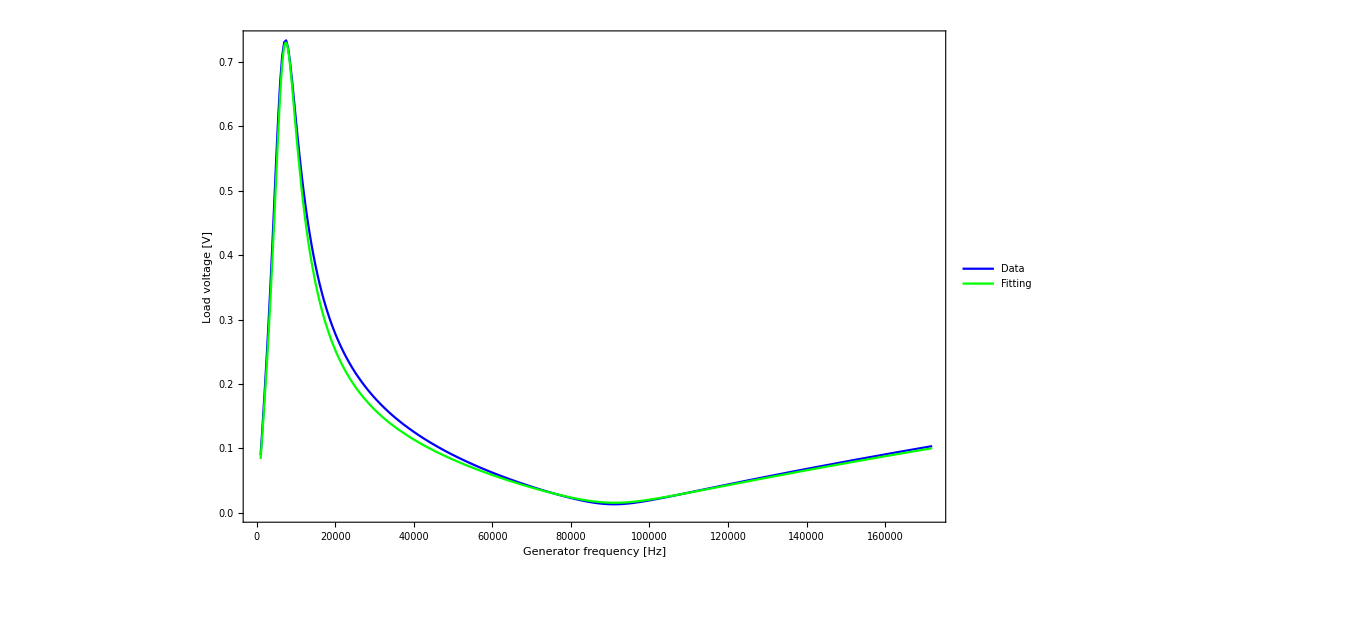

```mathematica
Legended[Show[ListLinePlot[newtable1, PlotStyle->Blue, PlotRange->Full],
Plot[Uin1[ω,10^-7,10^7,19],{ω,Min[newtable1[[All,1]]],Max[newtable1[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
Z3[ω_,Cb_,Rp_,Cp_,Ca_,L_]:=46.5+Zparallel2[(ⅈ×ω×5.39×10^-7+ZparallelRC[3.28×10^7,Cb, ω]+5.77+Zparallel3[50×10^3, (ⅈ×ω×L+0.5+ZparallelRL[Rp,0.0011,ω]), (1/(ⅈ×ω×Cp))]),(ⅈ×ω×9.83×10^-7+ZparallelRC[4.63×10^5, Ca, ω]+48)]+ZparallelRC[46.5, 25×10^-12, ω]
Uin3[ω_,Ca_,Cb_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[Z3[2π×ω,Cb,236,4×10^-11,Ca,0.00203]]]
```

```mathematica
fit3 = FindFit[newtable3, Uin3[ω,Ca,Cb], {{Ca,150×10^-12},{Cb,1.5×10^-9}}, ω, MaxIterations->1000]
```

FindFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

{Ca→1.56252×10^-10,Cb→1.38833×10^-9}

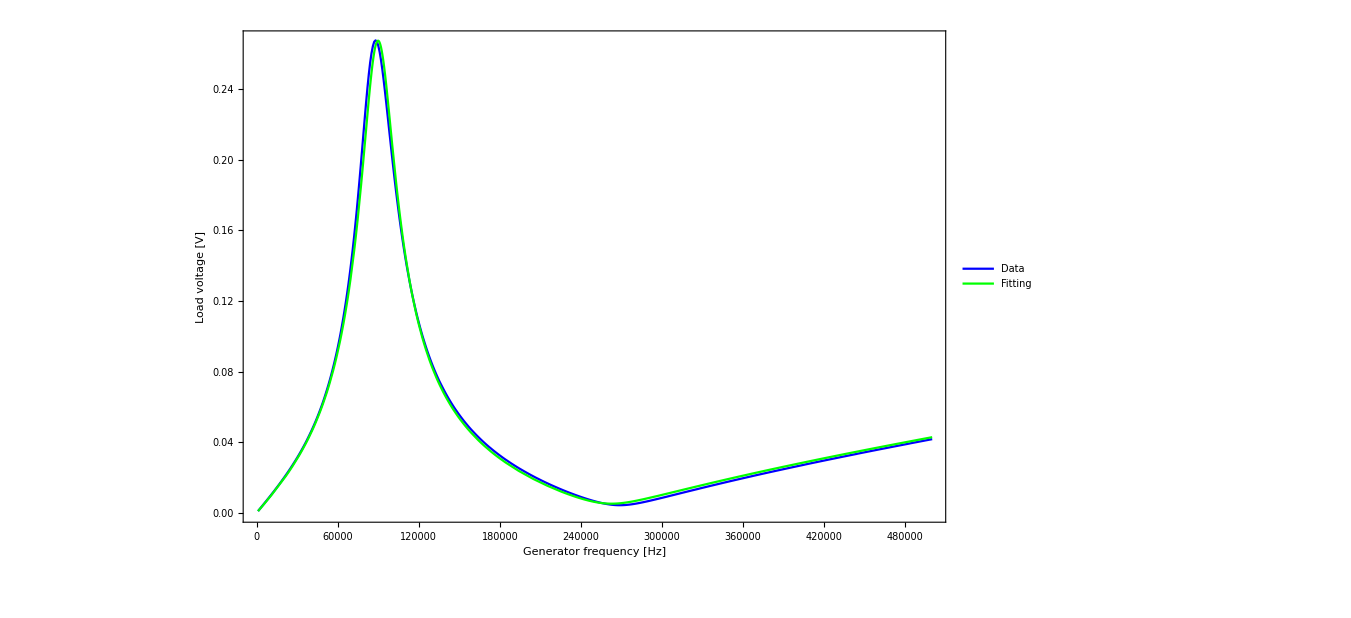

```mathematica
Legended[Show[ListLinePlot[newtable3, PlotStyle->Blue, PlotRange->Full],
Plot[Uin3[ω,Ca,Cb]/.fit3,{ω,Min[newtable3[[All,1]]],Max[newtable3[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->1000, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```

```mathematica
Z2[ω_,Cb_,Rp_,Cp_,Ca_,L_]:=46.5+Zparallel2[(ⅈ×ω×9.83×10^-7+ZparallelRC[4.63×10^5, Ca, ω]+48+Zparallel3[50×10^3, (ⅈ×ω×L+0.5+ZparallelRL[Rp,0.0011,ω]), (1/(ⅈ×ω×Cp))]),(ⅈ×ω×5.39×10^-7+ZparallelRC[3.28×10^7,Cb, ω]+5.77)]+ZparallelRC[46.5, 25×10^-12, ω]
Uin2[ω_,Ca_,Cb_]:=2*Re[Abs[ZparallelRC[46.5, 25*10^-12, 2π×ω]]/Abs[Z2[2π×ω,Cb,150,4.6×10^-11,Ca,0.00203]]]
```

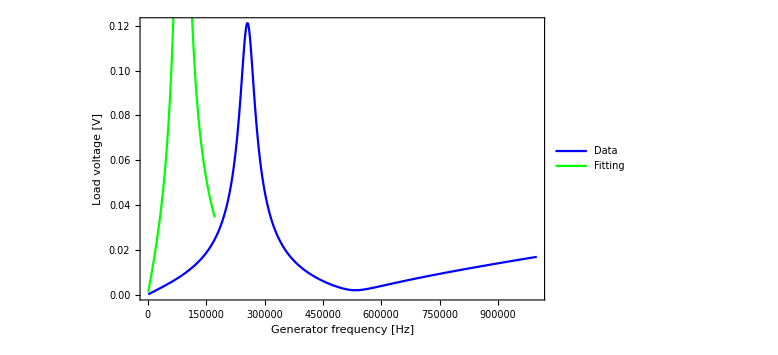

```mathematica
Legended[Show[ListLinePlot[newtable2, PlotStyle->Blue, PlotRange->Full],
Plot[Uin2[ω,1.5×10^-9,150×10^-12],{ω,Min[newtable1[[All,1]]],Max[newtable1[[All,1]]]},PlotStyle->Green, PlotRange->Full],  Frame->{True,True,False,False},FrameLabel->{"Generator frequency [Hz]","Load voltage [V]"},ImageSize->Large, BaseStyle->{FontSize->18}],LineLegend[{Blue, Green},{"Data", "Fitting"}]]
```